# Draw pictures for REED.tex on betweenness

```mathematica
dir=SetDirectory[NotebookDirectory[]];
NotebookEvaluate[dir<>"/lib/pow-reed.nb"]
```

Defines
title=Princess of Wales Hospital blood glucometer case
authors=Harold Thimbleby
version=v3
date=10 September 2025
and: communities, edges, groups, highlights, keywords, notes, vertexNames

Defines
title=Princess of Wales Hospital blood glucometer case
authors=Harold Thimbleby\nversion=v3
date=10 September 2025
and: communities, edges, groups, highlights,  keywords, vertexNames

Replicate  edges x -> y if x or y in groups

```mathematica
nameExpand=Map[("name"->"nodes")/.#&,groups];expandRule[u_->v_]:=Module[{ul=u/.nameExpand,vl=v/.nameExpand},
Outer[Rule,If[Head[ul]===List,ul,{ul}],If[Head[vl]===List,vl,{vl}]]
]
expandedEdges=Flatten@Map[expandRule,edges]
```

{Abbott_engineer→unknownEdits,forensicProblems→11,manual→7,unknownEdits→7,7→6,6→7,6unknown→6,backups→9,9→backups,backups→7,7→backups,9→3,3→9,8→9,9→8,7→8,8→7,5→7,4→5,17→18,16→17,16→18,14→15,unknownEdits→14,backups→14,9→14,8→14,7→14,6unknown→14,6→14,5→14,4→14,10→14,13→unknownEdits,13→backups,13→9,13→8,13→7,13→6unknown,13→6,13→5,13→4,13→10,13→14,11→12,7→11,7→10,6→8,8→6,1→6,2→4,1→4,1→3}

```mathematica
Graph[expandedEdges]
```

-Graphics-

```mathematica
g=Graph@expandedEdges
```

-Graphics-

```mathematica
vlist=VertexList[expandedEdges]
```

{Abbott_engineer,unknownEdits,forensicProblems,11,manual,7,6,6unknown,backups,9,3,8,5,4,17,18,16,14,15,10,13,12,1,2}

```mathematica
TextWords["hello world"]
```

{hello,world}

```mathematica
b=Map[Length[TextWords[#/.notes]]&,vlist]
```

{127,79,172,185,34,120,86,43,56,69,88,99,60,99,102,13,141,28,45,45,70,73,9,8}

```mathematica
vlist[[1]]/.notes
```

\warn{Mr\@. Nick Reece, a PrecisionWeb support Specialist employed by Abbott Diabetes Care, had been asked by the hospital to help when the Princess of Wales PrecisionWeb database faced problems in 2013. Mr.\ Reece then worked unsupervised on the PrecisionWeb database, apparently taking no notes and certainly not following any forensic process.}

Reece gave evidence that he had failed to take notes on exactly what he did when editing, deleting, and modifying data in the PrecisionWeb database. He admitted he had deleted critical data, which would have created the impression that nurses had been negligent not performing blood glucose tests.

\warn{This deletion of computer evidence explains the discrepancy in patient records that the prosecution claims had been wholly and entirely caused by the nurses' criminal negligence.}

```mathematica
b=Map[Length[TextWords#]&,vlist]
```

{2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2}

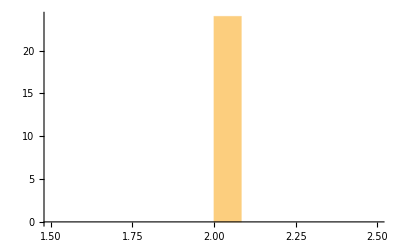

```mathematica
Histogram[b,12]
```

```mathematica
Thread[vlist-> b]
```

{Abbott_engineer→2,unknownEdits→2,forensicProblems→2,11→2,manual→2,7→2,6→2,6unknown→2,backups→2,9→2,3→2,8→2,5→2,4→2,17→2,18→2,16→2,14→2,15→2,10→2,13→2,12→2,1→2,2→2}

Show how much has been written for each node :

```mathematica
HighlightGraph[g,vlist,VertexSize->Thread[vlist-> Rescale[b]]]
```

-Graphics-

```mathematica
bg=Map[Module[{b,g,max,maxi,vlist},
b=BetweennessCentrality[g=Subgraph[expandedEdges,#]];
max=Max[b];
If[Length[Position[b,max]]==1,
maxi=Position[b,max][[1,1]];
vlist=VertexList[g];
Print[vlist[[maxi]]/.vertexNames];
vlist=vlist/.vlist[[maxi]]->Style[vlist[[maxi]],Darker[Red]];
Print[vlist];
];
Print[b^2];
HighlightGraph[g,vlist,VertexSize-> Thread[VertexList[g]-> Rescale[b^.9]],
VertexLabels->{"7"->Placed[Style["PrecisionWeb\ndatabase",20,Bold,Black],{-1.2,-.5}]}]
]&,WeaklyConnectedComponents[expandedEdges]];
```

v2-5.2 Abbott
PrecisionWeb
database

{backups,9,7,13,14,3,8,manual,unknownEdits,6,5,11,10,6unknown,4,15,1,Abbott_engineer,forensicProblems,12,2}

{121.,506.25,6006.25,0.,256.,2.25,289.,0.,121.,210.25,324.,256.,0.,0.,196.,0.,0.,0.,0.,0.,0.}

{0.,0.,0.}

```mathematica
betweennessplot=Show[{Show[bg[[1]],ImageSize->1000],Show[bg[[2]],ImageSize->50]}]
```

-Graphics-

```mathematica
Export["../REED-paper/figures/betweenness.png",betweennessplot]
```

../REED-paper/figures/betweenness.png

```mathematica
3580*1.2
```

4296.

## Now try and infer relations between highlights and keyword

A keyword implies a color if all nodes with that keyword have that color
A color implies a keyword if all nodes with that color have that keyword
A color and keyword are equivalent if the color implies the keyword and the keyword implies the color

```mathematica
allnodes=Union@Flatten[edges/.Rule->List]
```

{1,10,11,12,13,14,15,16,17,18,2,3,4,5,6,6unknown,7,8,9,Abbott_engineer,backups,forensicProblems,hospital,manual,unknownEdits}

```mathematica
allhighlights=Union[highlights/.(_->color_)->color]
```

{blue,none,red,white,yellow}

```mathematica
allkeywords=Union@Flatten[Union[keywords/.(_->keyword_)->keyword]]
```

{Audit,Backups,Corruption of evidence,CSV,Cybersecurity,Error logs,PrecisionWeb database,Testing}

```mathematica
generalisedKeywords=Append[keywords,_->{}]
```

{unknownEdits→{PrecisionWeb database},manual→{PrecisionWeb database},forensicProblems→{CSV,Cybersecurity,Backups,PrecisionWeb database},backups→{Backups,PrecisionWeb database},Abbott_engineer→{Corruption of evidence,PrecisionWeb database},9→{Error logs,PrecisionWeb database},8→{Error logs,PrecisionWeb database,Testing},7→{PrecisionWeb database},6unknown→{PrecisionWeb database},6→{},5→{Testing},4→{},3→{},2→{},18→{},17→{PrecisionWeb database},16→{PrecisionWeb database},15→{Audit,Error logs},14→{PrecisionWeb database,Testing},13→{},12→{},11→{CSV,PrecisionWeb database},10→{PrecisionWeb database},1→{},_→{}}

```mathematica
highlightof[node_]:=node/.highlights;
keywordsof[node_]:=node/.generalisedKeywords;
highlightednodes[color_]:=Cases[{#,highlightof@#}&/@allnodes,{node_,color}->node];
keywordednodes[keyword_]:=DeleteCases[Map[Module[{},
If[MemberQ[keywordsof[#],keyword],#,{}]
]&,allnodes],{}]
highlightof/@keywordednodes["Audit"]
```

{yellow}

```mathematica
highlightednodes["yellow"]
```

{14,15,6unknown,8,9,backups,forensicProblems,unknownEdits}

Find intersection of keywords for all nodes of highlight h

```mathematica
highlightof/@allnodes
```

{none,red,red,red,white,yellow,yellow,red,none,red,white,white,white,white,white,yellow,red,yellow,yellow,blue,yellow,yellow,none,none,yellow}

```mathematica
ColumnForm@DeleteCases[Map[Implies[#,Intersection@@Map[keywordsof,highlightednodes[#]]]&,allhighlights],Implies[_,{}]]
```

blue⇒{Corruption of evidence,PrecisionWeb database}

```mathematica
ColumnForm@DeleteCases[Map[Implies[#,Intersection@@List/@Map[highlightof,keywordednodes[#]]]&,allkeywords],Implies[_,{}]]
```

Audit⇒{yellow}
Backups⇒{yellow}
Corruption of evidence⇒{blue}
Cybersecurity⇒{yellow}
Error logs⇒{yellow}

```mathematica
keywordednodes["Corruption of evidence"]
```

{Abbott_engineer}

```mathematica
{"Abbott_engineer"}
```

{Abbott_engineer}

```mathematica
keywordsof/@%
```

{{Corruption of evidence,PrecisionWeb database}}

```mathematica
keywordednodes["PrecisionWeb database"]
```

{10,11,14,16,17,6unknown,7,8,9,Abbott_engineer,backups,forensicProblems,manual,unknownEdits}

```mathematica
8192*18/8./2^20
```

0.0175781

```mathematica
3456*2234
```

7720704